```mathematica
ClearAll[A,Γ,λ,Δ,r]
```

(0.000339703 Δ^0.5 ((A ⅈ_s)/P)^0.5)/(Γ λ)

4 Sin[0.5 θ]^2+(Cos[0.5 θ]^2-Sin[0.5 θ]^2)^0.5 η_la[P,Δ,r]

ⅇ^((1.80481×10^19 P (-0.250761-0.000209247 (r^2/P)^0.5 Δ^0.5) τ)/(r^2 Δ^2)) (1-ⅇ^(-(1.48647×10^-39 P^2 τ)/(No r^4 Δ^2)))^No

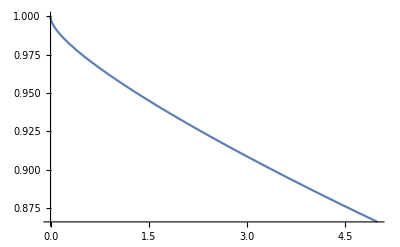

-Graphics-

(1-ⅇ^(-1.10623×10^-52 P^2))^2

```mathematica
ClearAll[No]
nm =10^(-9);MHz=10^6;GHz=10^9;mm=10^(-3);ms=10^(-3);
A=4*Pi*r*r; (*Area*)
Subscript[I, sat]=30.5 ;(*Saturation intensity (SI unit)*)
λ=780nm; (*wavelength*)
k=2*Pi/λ;(*wavevector*)
Γ=2*Pi*6.065MHz;
ℏ =1.054571 *10^(-34);
m= 1.4431*10^(-25);
Er = 4*ℏ*ℏ*k*k*0.5/m;
ωr = Er/ℏ;

theta=29*Pi/180;
detuning=100GHz;
radius=5mm;
n=2;
acctime=1ms;

Subscript[R, sc][P_,Δ_,r_]=(Γ*0.5*(P/(A*Subscript[I, sat])))/((2Δ/Γ)^2); (*Scattering rate due to spontaneous emissio*)
Subscript[η, lat][P_,Δ_,r_]=(2*2*Pi/(Γ*λ))((ℏ*Δ/m)^0.5)((Subscript[I, sat]*A/P)^0.5);(*Suppression factor*)
Subscript[η, tot][P_,Δ_,r_,θ_]= 4((Sin[0.5*θ])^2) + Subscript[η, lat][P,Δ,r]((((Cos[0.5*θ])^2)-((Sin[0.5*θ])^2))^0.5);(*Imperfect standing wave with θ angle*)
Subscript[F, sp][P_,Δ_,r_,θ_,τ_]= Exp[-Subscript[η, tot][P,Δ,r,theta]*Subscript[R, sc][P,Δ,r]*τ];(*Fraction surviving the launch despite of spontaneous emission loss*)

Vo[P_,Δ_,r_]=0.5*ℏ*Γ*(P/(A*Subscript[I, sat]))(1/(Δ/Γ));
Subscript[Ω, eff][P_,Δ_,r_]= Vo[P,Δ,r]*ωr*0.5;
α[No_,τ_]=No*ωr/τ;
Subscript[F, LZ][No_,P_,Δ_,τ_,r_]=(1-Exp[-0.5*Pi*((Subscript[Ω, eff][P,Δ,r])^2)/α[No,τ]])^No;
Frac[P_]=1;
Ftot[P_,Δ_,r_,θ_,τ_,No_,r_]=(Subscript[F, sp][P,Δ,r,θ,τ])*(Subscript[F, LZ][No,P,Δ,τ,r])

Plot[Ftot[P,detuning,radius,theta,acctime,n],{P,0,5}];
Plot[(Subscript[F, sp][P,detuning,radius,theta,acctime]),{P,0,5},PlotRange->All]
Plot[(Subscript[F, LZ][n,P,detuning,acctime]),{P,0,5},PlotRange->All]

(Subscript[F, LZ][n,P*Subscript[I, sat],detuning,acctime,radius])
```

```mathematica
Simplify[ⅇ^(0.00802139332380969 (0.-1.0613054571459644 (1/P)^0.5) P) (1-ⅇ^(-1.468113808054939*^-57 P^2))^2]
```

ⅇ^(-0.00851315/(1/P)^0.5-2.93623×10^-57 P^2) (-1+ⅇ^(1.46811×10^-57 P^2))^2

```mathematica
Vo[1,detuning,radius]
Subscript[Ω, eff][0,detuning,radius]
```

8.87922×10^-30

0.

```mathematica
Plot[(1-ⅇ^(-1.365712869943107*^-54 P^2))^2,{P,0,0.}]
```

Plot::plld: Endpoints for P in {P,0,0} must have distinct machine-precision numerical values.

Plot[(1-ⅇ^(-1.36571×10^-54 P^2))^2,{P,0,0}]

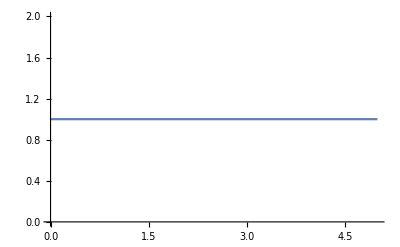

```mathematica
Plot[Exp[-10^(-54)x^2],{x,0,5}]
```

```mathematica
N[1/ⅇ^(1/1000000000000000000000000000000000000000000000000000000)]
```

1.